## Interraction of two bar magnets

```mathematica
Fmagn[x_]:= (B0^2 A^2(L^2+R^2))/(π μ0 L^2)(1/x^2+1/(x+2L)^2-2/(x+L)^2)
```

```mathematica
μ0 = 1.26*10^-6;
B0 = 0.3;
R = 13.05/2*10^-3;
A = π R^2;
L = 6.55*10^-3; 
m = 7.75*10^-3 ; (*mass of the magnet*)
l = 0.24; (*distance between the magnet and the rotational origin*)
```

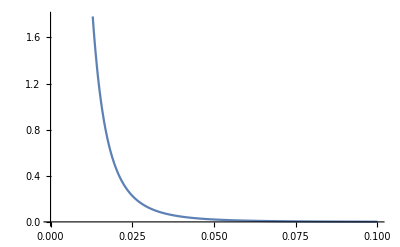

```mathematica
Plot[Fmagn[x],{x, 0, 0.1}]
```

## Force of a leaf spring

```mathematica
Ls = 0.50;
h = 0.6*10^-3;
b=2.8*10^-2;
Em = 370*10^9;
M = (150.74*10^-3)/1.03*Ls; (*mass of the oscillating part of the ruler*)
Fspring[s_]:=(b Em h^3 s)/(Ls^3 4)(*Лцчше писать нижу формлу чем значения ее симолов*)
Inertia = (M Ls^2)/3+m l^2
```

0.0065443

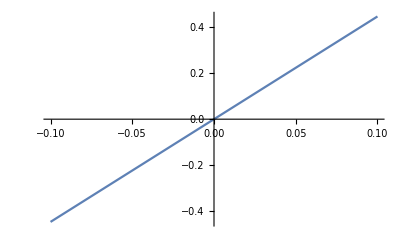

```mathematica
Plot[Fspring[x], {x, -0.1, 0.1}]
```

```mathematica
xLeft0 = -0.089;
xRight0 = -0.015;
k = 1.4;
```

```mathematica
s= NDSolve[{xLeft[0] == -0.142, xRight[0] == xRight0, xRight'[0] == 0, xLeft'[0] == 0,xRight''[t]/l == -(Fspring[xRight[t]-xRight0] * Ls)/Inertia+ (Fmagn[xRight[t] - xLeft[t]]*l)/Inertia - k xRight'[t], 
xLeft''[t]/l == -(Fspring[xLeft[t]-xLeft0]*Ls)/Inertia-(Fmagn[xRight[t] - xLeft[t]]*l)/Inertia -k xLeft'[t]},
 {xLeft, xRight},{t, 0, 50}]
```

{{xLeft→InterpolatingFunction[…],xRight→InterpolatingFunction[…]}}

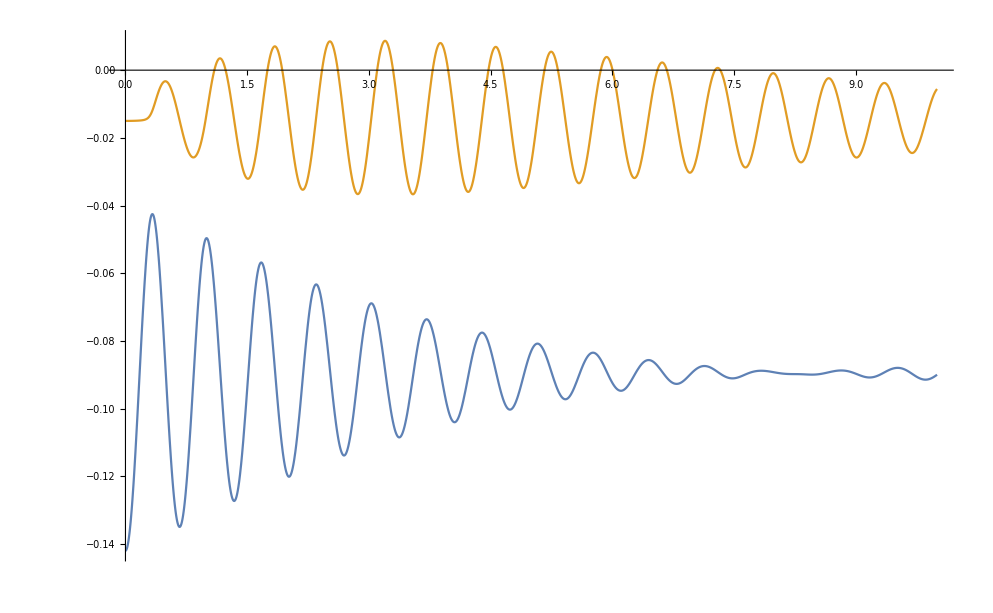

```mathematica
Plot[{xLeft[t]/.s,xRight[t]/.s}, {t, 0, 10}]
```

## Frequencies

```mathematica
freqByLinTheory = {{0.5, 1.5},{0.4, 2.5},{0.35, 3.5},{0.25, 6.84}, {0.2, 8.5}, {0.15, 17}};
freqByLinExp = {{0.35, 3.8}, {0.25, 6.8}, {0.2, 10}, {0.15, 17.4}};
```

```mathematica
fitTheory = Fit[freqByLinTheory, {1,x,x^2,x^3}, x]
```

59.9638-435.839 x+1118.85 x^2-962.941 x^3

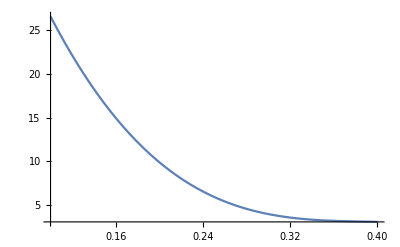

```mathematica
Plot[fitTheory, {x, 0.1, 0.4}]
```

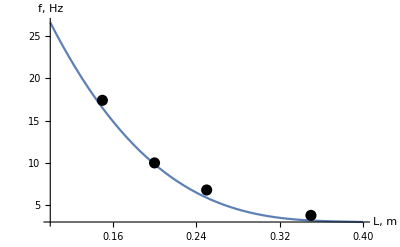

```mathematica
Show[Plot[fitTheory, {x, 0.1, 0.40}], ListPlot[freqByLinExp, PlotStyle->{Black, PointSize[0.02]} ], AxesStyle-> Directive[Black, 12], AxesLabel-> {"L, m", "f, Hz"}]
```